1

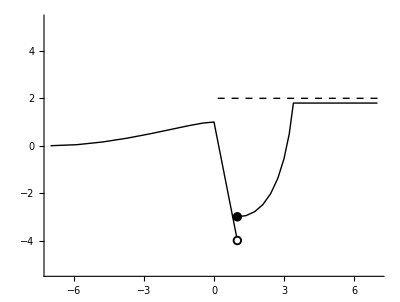

\documentclass{ximera}
\input{../preamble.tex}
\author{Bart Snapp}
\license{Creative Commons 3.0 By-NC}
\begin{document}
\begin{exercise}
\outcome{Understand what information the derivative gives concerning when
  a function is increasing or decreasing.}
\outcome{Understand what information the second derivative gives
  concerning concavity of a function.}
\outcome{Interpret limits as giving information about functions.}
\outcome{Determine how the graph of a function looks based on an analytic
  description of the function.}
  Sketch the graph of a function $f$ which has the following properties:
\begin{itemize}
  \item $f(0)=0$
  \item $\lim_{x \to 10^+} f(x) = +\infty$
  \item $\lim_{x \to 10^-} f(x) = -\infty$
  \item $f'(x)<0$ on $(-\infty,0) \cup (6,10) \cup (10,14)$
  \item $f'(x)>0$ on $(0,6) \cup (6,10) \cup (14,\infty)$
  \item $f''(x)<0$ on $(4,10)$
  \item $f''(x)>0$ on $(-\infty,4) \cup (10,\infty)$
  \item $\lim_{x\to\infty} f(x) = ?$
  \item $\lim_{x\to -\infty f(x) = ?&
  \end{itemize}
\begin{hint}
\begin{image}
\includegraphics[width=.5\textwidth]{solutionPlot1.png}
\end{image}
\end{hint}
\end{exercise}
\end{document}

```mathematica
numSections=4;

(*We start by making the middle of the domain*)
midDomain=Sort[RandomSample[{-4,-3,-2,-1,0,1,2,3,4},numSections-1]];

(*next we decide where the intersting point is*)
whereMid=2; (*it would be nice if this could change!*)

(*now we split the mid domain, and add endpoints of +- 7*) 
(*If[RandomInteger[{0,1}]==1,
leftDomain=ReplacePart[Join[{-7},Take[midDomain,whereMid]],2->midDomain[[whereMid+1]]];
rightDomain=Join[Take[midDomain,whereMid-numSections],{7}],*)
leftDomain=Join[{-7},Take[midDomain,whereMid]];
rightDomain=ReplacePart[Join[Take[midDomain,whereMid-numSections],{7}],1->midDomain[[whereMid]]];
(*];*)


(*We do something similar for the range*)
allRange=RandomSample[{-5,-4,-3,-2,-1,0,1,2,3,4,5},numSections+1];

leftRange=ReplacePart[Take[allRange,whereMid+1],(whereMid+1)->RandomChoice[{-4,-2,-0,2,4}]];
rightRange=ReplacePart[Take[allRange,whereMid-numSections-1],1->RandomChoice[{-3,-1,1,3}]];


(*The "start" and "finish" are ordered pairs that our curves start and finish at*)
startLeft=Table[{leftDomain[[i]],leftRange[[i]]},{i,1,numSections-whereMid}];
finishLeft=Table[{leftDomain[[i]],leftRange[[i]]},{i,2,numSections-whereMid}];
startRight=Table[{rightDomain[[i]],rightRange[[i]]},{i,1,numSections-whereMid-1}];
finishRight=Table[{rightDomain[[i]],rightRange[[i]]},{i,2,numSections-whereMid}];

(*Constructs two generic increasing control and node pts,
then will pick one at random*)
increasingConcaveUp = {{0,0},{.5,0},{1,1}};
increasingConcaveDown = {{0,0},{.5,1},{1,1}};
increasing:=RandomChoice[{increasingConcaveUp,increasingConcaveDown}];

(*Constructs two generic decreasing control and node pts,
then will pick one at random*)
decreasingConcaveUp = {{0,0},{.5,-1},{1,-1}};
decreasingConcaveDown = {{0,0},{.5,0},{1,-1}};
decreasing:=RandomChoice[{decreasingConcaveUp,decreasingConcaveDown}];

negHorizontalAsymptoteDecreasing={{0,0},{9/10,0},{1,-1}} ;
negHorizontalAsymptoteIncreasing={{0,0},{9/10,0},{1,1}} ;

posHorizontalAsymptoteDecreasing={{0,0},{1/10,-1},{1,-1}} ;
posHorizontalAsymptoteIncreasing={{0,0},{1/10,1},{1,1}} ;

(*This shifts and scales pts*)
shifter[start_,finish_,pt_]:=Module[{},
scalars={Abs[(finish-start)[[1]]],Abs[(finish-start)[[2]]]};
Map[start+scalars*# &,pt]];


glue[listOfParts_]:=DeleteDuplicates[Join[Flatten[listOfParts,1]]];

whereHorizAsym=RandomInteger[{0,1}]; (* 0 is on the left, 1 on the right*)
If[whereHorizAsym==0,
(*When Horiz Asy is on left*)
horizAsym=
If[leftRange[[2]]-leftRange[[1]]>0,
shifter[{leftDomain[[1]],leftRange[[1]]+2/10},{leftDomain[[2]],leftRange[[2]]},negHorizontalAsymptoteIncreasing],
shifter[{leftDomain[[1]],leftRange[[1]]-2/10},{leftDomain[[2]],leftRange[[2]]},negHorizontalAsymptoteDecreasing]],
(*When Horiz Asy is on right*)
horizAsym=If[rightRange[[numSections-whereMid+1]]-rightRange[[numSections-whereMid]]>0,shifter[{rightDomain[[numSections-whereMid]],rightRange[[numSections-whereMid]]},{rightDomain[[numSections-whereMid+1]],rightRange[[numSections-whereMid+1]]-2/10},posHorizontalAsymptoteIncreasing],
shifter[{rightDomain[[numSections-whereMid]],rightRange[[numSections-whereMid]]},{rightDomain[[numSections-whereMid+1]],rightRange[[numSections-whereMid+1]]+2/10},posHorizontalAsymptoteDecreasing]]];


(*Since we are concatinating the asymptotes, we need to adjust the end pts for the next part*)
beginLeft=If[whereHorizAsym==0,2,1];
endLeft=If[whereHorizAsym==0,numSections-whereMid+1,numSections-whereMid+1];

beginRight=If[whereHorizAsym==0,1,1];
endRight=If[whereHorizAsym==0,numSections-whereMid,numSections-whereMid-1];

leftPrePointParts=Table[
If[leftRange[[i+1]]-leftRange[[i]]>0,shifter[{leftDomain[[i]],leftRange[[i]]},{leftDomain[[i+1]],leftRange[[i+1]]},increasing],
shifter[{leftDomain[[i]],leftRange[[i]]},{leftDomain[[i+1]],leftRange[[i+1]]},decreasing]]
,{i,beginLeft,endLeft-1}];

rightPrePointParts=Table[
If[rightRange[[i+1]]-rightRange[[i]]>0,shifter[{rightDomain[[i]],rightRange[[i]]},{rightDomain[[i+1]],rightRange[[i+1]]},increasing],
shifter[{rightDomain[[i]],rightRange[[i]]},{rightDomain[[i+1]],rightRange[[i+1]]},decreasing]]
,{i,beginRight,endRight}];


If[whereHorizAsym==0,
leftPointParts=Prepend[leftPrePointParts,horizAsym];
rightPointParts=rightPrePointParts,
leftPointParts=leftPrePointParts;
rightPointParts=Append[rightPrePointParts,horizAsym]];


(*increasing concave up*)
leftIncreasingConcaveUp=(leftPointParts[[numSections-whereMid,3,2]]-leftPointParts[[numSections-whereMid,1,2]]>0 
&& 
leftPointParts[[numSections-whereMid,2,2]]==leftPointParts[[numSections-whereMid,1,2]]);

(*deceasing concave down*)
leftDecreasingConcaveDown=(leftPointParts[[numSections-whereMid,3,2]]-leftPointParts[[numSections-whereMid,1,2]]<0 
&& 
leftPointParts[[numSections-whereMid,2,2]]==leftPointParts[[numSections-whereMid,1,2]]);

(*increasing concave down*)
rightIncreasingConcaveDown=(rightPointParts[[1,3,2]]-rightPointParts[[1,1,2]]>0 
&& 
rightPointParts[[1,2,2]]==rightPointParts[[1,3,2]]);
(*deceasing concace up*)
rightDecreasingConcaveUp=(rightPointParts[[1,3,2]]-rightPointParts[[1,1,2]]<0 
&& 
rightPointParts[[1,2,2]]==rightPointParts[[1,3,2]]);

(*0 two open holes;*)
(*1 open jume to new value;*)
(*2 left open hole, right closed hole;*)
(*3 left closed hole, right open hole;*)
(*4 vert asy *)
If[Or[leftIncreasingConcaveUp,leftDecreasingConcaveDown,rightIncreasingConcaveDown,rightDecreasingConcaveUp],
vadSelector=RandomInteger[{2,4}],vadSelector=RandomInteger[{0,3}]];



If[And[vadSelector==4,leftIncreasingConcaveUp],leftPointParts[[numSections-whereMid,3,2]]=8;
leftPointParts[[numSections-whereMid,2,1]]=leftPointParts[[numSections-whereMid,3,1]]-.2
];
If[And[vadSelector==4,leftDecreasingConcaveDown],leftPointParts[[numSections-whereMid,3,2]]=-8;
leftPointParts[[numSections-whereMid,2,1]]=leftPointParts[[numSections-whereMid,3,1]]-.2
];

If[And[vadSelector==4,rightIncreasingConcaveDown],rightPointParts[[1,1,2]]=8;
rightPointParts[[1,2,1]]=rightPointParts[[1,1,1]]+.2
];
If[And[vadSelector==4,rightDecreasingConcaveUp],rightPointParts[[1,1,2]]=-8;
rightPointParts[[1,2,1]]=rightPointParts[[1,1,1]]+.2
];


horizAsymLine=If[whereHorizAsym==0,
Line[{{leftDomain[[1]],leftRange[[1]]},{0,leftRange[[1]]}}],
Line[{{rightDomain[[numSections-whereMid+1]],rightRange[[numSections-whereMid+1]]},{0,rightRange[[numSections-whereMid+1]]}}]];

r=.2;
(*0 two open holes;*)
(*1 open jume to new value;*)
(*2 left open hole, right closed hole;*)
(*3 left closed hole, right open hole;*)
(*4 vert asy *)

(*0 two open holes;*)
vertAsyDis[0]:={
Thick, Disk[{Last[leftDomain],Last[leftRange]},r],
Thick, Disk[{First[rightDomain],First[rightRange]},r],
White, Disk[{Last[leftDomain],Last[leftRange]},.6*r],
White, Disk[{First[rightDomain],First[rightRange]},.6*r]};
(*1 open jume to new value;*)
vertAsyDis[1]:={
discValue=RandomChoice[Complement[{-5,-4,-3,-2,-1,0,1,2,3,4,5},{Last[leftRange],First[rightRange]}]];
Thick, Disk[{Last[leftDomain],discValue},r],
Thick, Disk[{Last[leftDomain],Last[leftRange]},r],
Thick, Disk[{First[rightDomain],First[rightRange]},r],
White, Disk[{Last[leftDomain],Last[leftRange]},.6*r],
White, Disk[{First[rightDomain],First[rightRange]},.6*r]};
(*2 left open hole, right closed hole;*)
vertAsyDis[2]:={
Thick, Disk[{Last[leftDomain],Last[leftRange]},r],
Thick, Disk[{First[rightDomain],First[rightRange]},r],
White, Disk[{Last[leftDomain],Last[leftRange]},.6*r]};
(*3 left closed hole, right open hole;*)
vertAsyDis[3]:={
Thick, Disk[{Last[leftDomain],Last[leftRange]},r],
Thick, Disk[{First[rightDomain],First[rightRange]},r],
White, Disk[{Last[leftDomain],Last[leftRange]},.6*r]};
(*4 vert asy *)
vertAsyDis[4]:={
{Thin,Dashed,Line[{{Last[leftDomain],-6},{Last[leftDomain],6}}]},
(*discValue=RandomChoice[Complement[{-5,-4,-3,-2,-1,0,1,2,3,4,5},{Last[leftRange],First[rightRange]}]];
Thick, Disk[{leftPointParts[[numSections-whereMid,3,1]],discValue},r],*)
Thick, Disk[leftPointParts[[numSections-whereMid,3]],r],
Thick, Disk[rightPointParts[[1,1]],r],
White, Disk[leftPointParts[[numSections-whereMid,3]],.6*r],
White, Disk[rightPointParts[[1,1]],.6*r]
}

THEPLOT=Graphics[{{Thick,BezierCurve[glue[leftPointParts],SplineDegree->2],Thick,BezierCurve[glue[rightPointParts],SplineDegree->2]},{Thin,Dashed,horizAsymLine},vertAsyDis[vadSelector]},Axes->True,PlotRange->{{-7,7},{-5.3,5.3}}];



i=1
THEPLOT
StringJoin["\\documentclass{ximera}
\\input{../preamble.tex}
\\author{Bart Snapp}
\\license{Creative Commons 3.0 By-NC}
\\begin{document}
\\begin{exercise}
\\outcome{Understand what information the derivative gives concerning when
  a function is increasing or decreasing.}
\\outcome{Understand what information the second derivative gives
  concerning concavity of a function.}
\\outcome{Interpret limits as giving information about functions.}
\\outcome{Determine how the graph of a function looks based on an analytic
  description of the function.}
  Sketch the graph of a function $f$ which has the following properties:
\\begin{itemize}
  \\item $f(0)=0$
  \\item $\\lim_{x \\to 10^+} f(x) = +\\infty$
  \\item $\\lim_{x \\to 10^-} f(x) = -\\infty$
  \\item $f'(x)<0$ on $(-\\infty,0) \\cup (6,10) \\cup (10,14)$
  \\item $f'(x)>0$ on $(0,6) \\cup (6,10) \\cup (14,\\infty)$
  \\item $f''(x)<0$ on $(4,10)$
  \\item $f''(x)>0$ on $(-\\infty,4) \\cup (10,\\infty)$
  \\item $\\lim_{x\\to\\infty} f(x) = ?$
  \\item $\\lim_{x\\to -\\infty f(x) = ?&
  \\end{itemize}
\\begin{hint}
\\begin{image}
\\includegraphics[width=.5\\textwidth]{solutionPlot",ToString[i],".png}
\\end{image}
\\end{hint}
\\end{exercise}
\\end{document}"]
```